```mathematica
(* Задача 1 *)
KroneckerVector[k_,n_]:=Table[KroneckerDelta[i,k],{i,1,n}]
GaussNewton[r_,p0_,tol_,maxIter_]:=Module[{iter=0,p=p0,riter=r[p0],ϵ=tol,J,h,n=Length@p0,KroneckerVectors,riterLast},
KroneckerVectors=ϵ Table[KroneckerVector[k,n],{k,1,n}];
riterLast=ConstantArray[0,Length@riter];

While[Norm[riter-riterLast]≥tol&&iter≤maxIter,
J=Transpose@Table[(r[p+KroneckerVectors⟦i⟧]-riter)/ϵ,{i,1,n}];
h=LeastSquares[J,-riter];
p=p+h;
{riterLast, riter}={riter,r[p]};
iter++;
];

p
]
CleanVector[l_,ϵ_]:=If[Abs@#≤ϵ,0,#]&/@l
(* The error function for tha parabola x^2+0x+0 *)
parabolaErr[{a_,b_,c_}]:={a -b+c - 1,c,a+b+c-1}
CleanVector[GaussNewton[parabolaErr,{1,0,3},0.004,15],10^-8]
```

2

{1.,0,0}

```mathematica
(* Задача 2 *)
FehlbergCoefficients[4, p_]:=Module[{
Fehlbergamat={
{1/4},
{3/32,9/32},
{1932/2197,-7200/2197,7296/2197},{439/216,-8,3680/513,-845/4104},{-8/27,2,-3544/2565,1859/4104,-11/40}
},
Fehlbergbvec={25/216,0,1408/2565,2197/4104,-1/5, 0},
Fehlbergcvec = {1/4,3/8,12/13,1,1/2},
Fehlbergevec={-1/360,0,128/4275,2197/75240,-1/50,-2/55}
},
N[{Fehlbergamat,Fehlbergbvec,Fehlbergcvec,Fehlbergevec}, p]
]
Fehlberg45 = {"ExplicitRungeKutta","Coefficients"->FehlbergCoefficients,"DifferenceOrder"->4,"EmbeddedDifferenceOrder"->5, "StiffnessTest"->False};
CRK4[]["Step"[rhs_, h_, t_, x_, xp_]] :=Module[{k0,k1,k2,k3},
k0=h xp;
k1=h rhs[t+h/2,x+k0/2];
k2=h rhs[t+h/2,x+k1/2];
k3=h rhs[t+h,x+k2];
(k0+2  k1+2  k2+k3)/6];
CRK4[___]["StepInput"] = {"F"["T","X"],"H","T","X","XP"};
CRK4[___]["StepOutput"] = "XI";
CRK4[___]["StepInput"] = {"Function"["Time","DependentVariables"],"TimeStep","Time","DependentVariables","TemporalDerivatives"};
CRK4[___]["StepOutput"] = "DependentVariablesIncrement";
CRK4[___]["DifferenceOrder"] := 4
CRK4[___]["StepMode"]:=Fixed
ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]];
RKPopulation={"FixedStep",Method->{"ExplicitRungeKutta","Coefficients"->ClassicalRungeKuttaCoefficients,"DifferenceOrder"->4,"StiffnessTest"->False}};
```

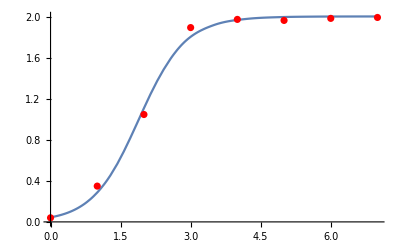

```mathematica
T=7;
tTable=Range[0,T];
u={0.04,0.35,1.05,1.9,1.98,1.97,1.99,1.999};

(*populationErr[{r_,k_}]:=NDSolve[{y'[t]==r y[t](1-y[t]/k), y[0]==Subscript[u, 0]},y[t],{t,0,T},Method->Fehlberg45]/@tTable-u*)
populationFunc[{u0_,r_,k_}]:=NDSolveValue[{y'[t]==r y[t](1-y[t]/k), y[0]==u0},y[t],{t,0,T},
Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}},StartingStepSize->0.8]
populationErr[{u0_,r_,k_}]:=Module[{yy=populationFunc[{u0,r,k}]},
(*interpolatedSolution/@tTable-u*)
Table[(yy/.{t->tTable⟦i⟧})-u⟦i⟧,{i,1,Length@u}]
]
bestParams=GaussNewton[populationErr,{First@u,2,2},10^-8,10];
bestApprox=populationFunc@bestParams;
Show[{
Plot[bestApprox/.{t->tt},{tt,0,T}],
ListPlot[Thread[{tTable,u}], PlotStyle->Red]
}]
```

```mathematica
(* Задача 3 *)
(*diffusion[{d_}]:=NDSolveValue[D[u[x,t],t]==d D[u[x,t],{x,2}],u[x,t],{x,0,1},{t,0,2},Method->{"FixedStep"}]*)
diffusion[xR_,T_,n_,d_]:=Module[{h=xR/n,τ,m,res,coeff},
τ=h^2/(4d);
(*m=Ceiling[T/τ];
τ=T/m;*)
τ=10^(Floor@Log10@τ);
m=T/τ;
coeff=N@((d τ)/h^2);
res=ConstantArray[0,{m+1,n+1}];

For[k=0,k≤n,k++,
res⟦1,k+1⟧=N@Sin[2 Pi k h];
];

For[j=1,j≤m,j++,
For[i=2,i≤n,i++,
res⟦j+1,i⟧=coeff(res⟦j,i-1⟧+res⟦j,i+1⟧)+(1-2 coeff)res⟦j,i⟧;
];
res⟦j+1,1⟧=0;
res⟦j+1,n+1⟧=0;
];

{res,Table[k τ,{k,0,m}],Table[k h,{k,0,n}]}
]
```

3

{0.00946959}

{0,1,2}

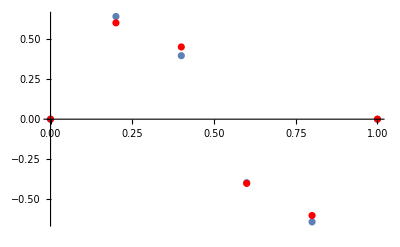

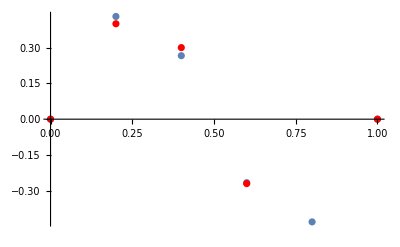

```mathematica
uGiven={{0,0.6,0.45,-0.4,-0.6,0},{0,0.4,0.3,-0.27,-0.47,0}};
diffusionErr[{d_}]:=Module[{res,tList,xList,oneIndex},
{res,tList,xList}=diffusion[1,2,5,d];
{oneIndex}=FirstPosition[tList,1];
Catenate[res⟦{oneIndex, Length@tList}⟧-uGiven]
]
(*Plot[Norm@diffusionErr[{x}],{x,0,0.01}, PlotRange->All]*)
{bestD}=GaussNewton[diffusionErr,{0.008},10^-4,15]
{bestApprox,tList,xList}=diffusion[1,2,5,bestD];
tList
{oneIndex}=FirstPosition[tList,1];
Show[{
ListPlot[Thread[{xList,bestApprox⟦oneIndex⟧}]],
ListPlot[Thread[{xList,uGiven⟦1⟧}],PlotStyle->Red]
}]
Show[{
ListPlot[Thread[{xList,bestApprox⟦Length@tList⟧}]],
ListPlot[Thread[{xList,uGiven⟦2⟧}], PlotStyle->Red]
}]
```

```mathematica
{res,tt,xx}=diffusion[1,2,5,0.3];
Manipulate[
ListPlot[res⟦k⟧, PlotRange->{{0,6},{-1,1}}],
{k,1,Length@tt,1}
]
Plot[0.011286177015393742]
```